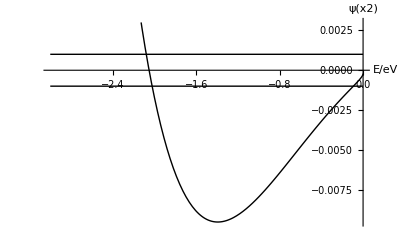

{e→-2.07927}

{e→-0.0930281}

```mathematica
V0=-3;a=2;α=0.262713;ψ0=10^-3;x0=2a;
V[x_]:=Which[Abs[x]≤a,V0,True,0]
f[e_?NumberQ]:=
Block[{ψ,x,x1=-x0,x2=x0},
First[ψ[x2]/.
NDSolve[{ψ''[x]+α(e-V[x])ψ[x]==0,ψ[x1]==ψ0,ψ'[x1]==√(-α(e-V[x1]))  ψ0},
ψ,{x,x1,x2}]]]
Plot[{f[e],ψ0,-ψ0},{e,V0,0},
PlotRange->{{-2.5,0.2},{3ψ0,-10ψ0}},
AxesLabel->{"E/eV","ψ(x2)"},
Epilog->{Text["ψ0",{0.1,ψ0}],Text["-ψ0",{0.1,-ψ0}]},
PlotStyle->Black,PlotPoints->100]
FindRoot[f[e]==ψ0,{e,-2.2,-2.0}]
FindRoot[f[e]==-ψ0,{e,-0.2,0}]
Clear["Global`*"]
```